InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

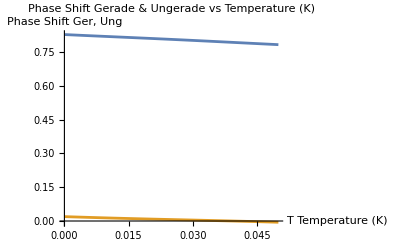

```mathematica
(* Reduced Mass *)
(* All atomic units *)
μ=1835;   
mP=1836;   (* Proton mass *)
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
(* 1 kelvin[K]=8.61732814974056E-05 electron-volt[eV]*)
(* 1 Hartree = 27.2114eV *)
R0 = 0.01; (* distance between nuclei, atomic units*)
 
(* Potential tables for the gerade and ungerade case *)
vSg1Data  = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];
vSu1Data = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx"];

(* Max value of R for calculation *)
maxR = 50;


(*vSg1Data = Prepend[vSg1Data,{0,-8.0, 10^100,25.8,0,.11}];
vSu1Data=Prepend[vSu1Data,{0,-0.889,  10^100,25.81,0.041}];*)

(* Interpolatte the potential *)
vGerade:=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}]];
vUngerade :=Interpolation[Transpose[{vSu1Data[[All,1]],vSu1Data[[All,3]]}]];

(* Calogero's differential equation to compute the phase shift delta *)
deltaPrime[vPotential_,r_,k_,m_,delta_]:=Module[{Jm,Ym,psi},
Jm=BesselJ[m,k*r];
Ym=BesselY[m,k*r];
psi=Jm*Cos[delta]-Ym*Sin[delta];
-vPotential[r]*psi^2/k
];

(* Calogero's method to compute the phase shift delta *)
delta[deltaPrime_,vPotential_,k_,m_]:=Module[{solDelta,deltaEq,deltaFinal},
(* Calogero *)
solDelta=NDSolve[{deltaEq'[r]==deltaPrime[vPotential,r,k-vPotential[50],m,deltaEq[r]],deltaEq[0.01]==0},deltaEq,{r,20,50}];

deltaFinal=deltaEq[50]/. solDelta[[1]]//N;

deltaFinal
];

(* Compute deltas for the gerade and ungerade case *)
deltaG[k_,m_]:= delta[deltaPrime,vGerade,k,m];
deltaU[k_,m_]:= delta[deltaPrime,vUngerade,k,m];

Plot[{deltaG[k,0]-deltaU[k,0]},{k,0,0.05},AxesLabel->{"T Temperature (K)","Phase Shift Ger, Ung"},PlotLabel->"Phase Shift Gerade & Ungerade vs Temperature (K)"]


eps[m_]:=If[ m==0,1,2];

(* Cross section *)
σ[k_,m_]:= 4/k Sum[eps[i](Sin[deltaG[k,i]-deltaU[k,i]])^2,{i,0,m}];
(* some constants for reference *)
(* 1K = 7.733675709525194*^-7 Hartree *)
(* 1 Subscript[a, 0] (Bohr radius = 5.29177210544*10^-11
1 barn = 10^-28
1 Subscript[a^2, 0]=5.29177210544*^-22 = 5.29177210544*^6 barn
 *)
(* Scattering at around room temperature, 270-310K *)
(* Subscript[k, B] = 3.167*10^−6  Subscript[E, H]/T (Boltzman) *) 
(* k = √((2mE)/ℏ)*)
(* 1 Subscript[E, H]=3.1577464 x 10^5 K *)
(* 270K = 0.000855 Subscript[E, H] => k = 0.0413531175145633 *)
(*300K = 0.00095 Subscript[E, H]=> k = 0.0435900132315404 *)
```

```mathematica
allSigma[m_] := Table[{k,σ[k,m]} ,{k,0.0413,0.04359,0.0001}];

(* Cross section in atomic units *)
 crossSections:=allSigma[0] ;

(* temp in Kelvins *)
crossSectionsK :=Transpose[{(crossSections[[All,1]]^2)*3.1577464*^5 /2,crossSections[[All,2]]}];
```

```mathematica
f=Interpolation[crossSectionsK,InterpolationOrder->2];
f[0.001]
```

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

101.662

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

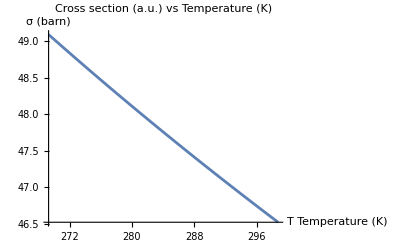

```mathematica
Plot[f[x],{x,crossSectionsK[[1,1]],crossSectionsK[[Length[crossSections],1]]},Epilog->Point[crossSections],AxesLabel->{"T Temperature (K)","σ (a.u.)"},
PlotLabel->"Cross section (a.u.) vs Temperature (K)"]
```